Проверка точности функции нормировки

```mathematica
Intω[ω_]:=With[{ωlocal=ω},
xl=leftCutOff[ωlocal];
xr=rightCutOff[ωlocal];
Dplus[x_]=Derivative[1,0,0][Duh][qplus[ωlocal,x],ωlocal,x];
Dminus[x_]=-Derivative[1,0,0][Duh][qminus[ωlocal,x],ωlocal,x];
δψ[x_?NumericQ]:=NIntegrate[qplus[ωlocal,ξ]-qminus[ωlocal,ξ],{ξ,xl,x}];
func[ξ_?NumericQ]:=1/Dplus[ξ]+1/Dminus[ξ]+(2 Sin[δψ[ξ]])/(√(Dplus[ξ]Dminus[ξ]));
func2[ξ_?NumericQ]:=1/Dplus[ξ]+1/Dminus[ξ];

{Ι,lazyint}={Re@NIntegrate[func[ξ],{ξ,xl,xr}],NIntegrate[func2[ξ],{ξ,xl,xr}]}
]
```

```mathematica
Table[Intω[ω],{ω,ωmin,0.99999ωmax,(-ωmin+0.99999ωmax)/100}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {2.5852926603802744400723314895703536242521636268065776675939559937}. NIntegrate obtained 10.1653-0.859153 ⅈ and 0.440926 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {2.5852926603802744400723314895703536242521636268065776675939559937}. NIntegrate obtained 9.76054-0.859153 ⅈ and 0.279566 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ξ near {ξ} = {3.4133538232639502336681953885924631394012222773692855071203666739}. NIntegrate obtained 1.98933-1.07589×10^-6 ⅈ and 0.0000123624 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{10.1653,9.76054-0.859153 ⅈ},{2.56619,2.22184},{2.12887,2.04236},{2.22651,1.93921},{1.95149,1.86715},{1.98933,1.81206-2.8873×10^-7 ⅈ},{1.96738,1.76765},{1.76424,1.73058},{1.93866,1.69886},{1.7693,1.67121},{1.70986,1.64675},{1.86483,1.62488-1.90232×10^-7 ⅈ},{1.65371,1.60512},{1.66972,1.58714},{1.80071,1.57066},{1.58788,1.55547},{1.61875,1.54141},{1.75537,1.52832},{1.55442,1.51611},{1.55497,1.50466},{1.71939,1.4939},{1.55145,1.48377},{1.48515,1.47419},{1.67336,1.46512},{1.57853,1.45651},{1.42861,1.44833},{1.59714,1.44054},{1.61987,1.43311},{1.41607,1.42601-3.55882×10^-7 ⅈ},{1.48906,1.41922-1.60582×10^-7 ⅈ},{1.63475,1.41272-2.03177×10^-7 ⅈ},{1.46814,1.40648},{1.38737,1.40049},{1.57634,1.39474},{1.5574,1.3892},{1.36141,1.38387},{1.44585,1.37873-2.21685×10^-7 ⅈ},{1.59695,1.37378},{1.44485,1.369},{1.33347,1.36438-8.13595×10^-7 ⅈ},{1.51082,1.35991},{1.55771,1.35559-2.26341×10^-7 ⅈ},{1.35581,1.35141-4.58532×10^-7 ⅈ},{1.35296,1.34736},{1.54701,1.34344},{1.49555,1.33963-3.43667×10^-7 ⅈ},{1.30298,1.33594},{1.38488,1.33236},{1.55555,1.32888},{1.43697,1.32551-1.41384×10^-7 ⅈ},{1.27599,1.32222},{1.41035,1.31903-2.90778×10^-7 ⅈ},{1.5494,1.31593},{1.39286,1.31291},{1.26112,1.30997},{1.42331,1.30711},{1.54013,1.30432-1.34875×10^-7 ⅈ},{1.36535,1.30161},{1.2488,1.29896-1.53996×10^-7 ⅈ},{1.42305,1.29638},{1.53428,1.29387},{1.35412,1.29141},{1.23473,1.28902},{1.40956,1.28668},{1.53355,1.2844},{1.35946,1.28218},{1.21929,1.28},{1.38184,1.27788},{1.53522,1.27581},{1.38267,1.27378},{1.20742,1.2718-1.30784×10^-7 ⅈ},{1.33868,1.26987},{1.53212,1.26798},{1.42426,1.26613},{1.20867,1.26432},{1.28144,1.26255},{1.51294,1.26082},{1.48046,1.25912},{1.23618,1.25746-2.21707×10^-7 ⅈ},{1.21826,1.25584},{1.46467,1.25426},{1.53882,1.2527-2.37096×10^-7 ⅈ},{1.30269,1.25118-3.99227×10^-7 ⅈ},{1.16836,1.24969-1.58221×10^-7 ⅈ},{1.37898,1.24824},{1.57556,1.24681},{1.41244,1.24541-1.76676×10^-7 ⅈ},{1.16291,1.24404},{1.26281,1.2427},{1.55922,1.24139-2.20665×10^-7 ⅈ},{1.55133,1.2401},{1.23893,1.23884-1.25901×10^-7 ⅈ},{1.14948,1.2376},{1.46485,1.23639},{1.68604,1.2352-1.32272×10^-7 ⅈ},{1.43146,1.23404},{1.10263,1.2329},{1.2983,1.23179},{1.83366,1.23069},{1.90923,1.22962},{1.25343,1.22856}}

```mathematica
data=%
```

```mathematica
data2=Table[ω2f@ω,{ω,ωmin,0.99999ωmax,(-ωmin+0.99999ωmax)/100}];
```

```mathematica
data4=Re/@{data2,data3}ᵀ;
```

```mathematica
data3=Map[(#⟦2⟧)/(#⟦1⟧)-1&,data];
```

```mathematica
meanabs=Mean@data3
meanrel=Total@Map[#⟦2⟧-#⟦1⟧&,data]
meanrel=Sqrt@Total@Map[(#⟦2⟧-#⟦1⟧)^2&,data]
```

-0.0723216-0.000836858 ⅈ

-12.4865-0.859159 ⅈ

1.68317+0.206578 ⅈ

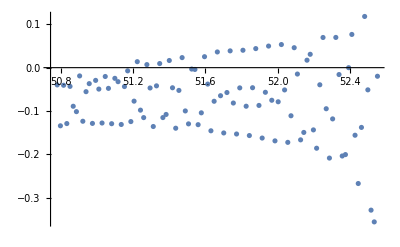

```mathematica
ListPlot@data4
```